```mathematica
Clear[d1]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
a1[x_, z_] := x^z
a2[x_, z_] := (x-1)^z
g1[ x_, z_] := LaguerreL[-z,Log[x]]
g1l[x_] := LogIntegral[x]-Log[Log[x]]-EulerGamma
g2[x_, z_] := (-1)^z Gamma[ z, 0, -Log[x]]/Gamma[z]
g2l[x_] := LogIntegral[x]
d1[x_,z_,k_:1]:=d1[x,z,k]=1+((z+1)/k-1) Sum[d1[x/j,z,k+1],{j,2,x}];d1[0,z_, k_] := 0;d1[0,z_] := 0
d2[x_, z_] := d2[x,z]=Sum[ d2[x/j,z-1], {j,2,x}]; d2[x_, 0] := UnitStep[x-1]
dd1[x_,z_] := d1[x,z]-d1[x-1,z]
dd2[x_,z_]:=d2[x,z]-d2[x-1,z]
g1lk[ n_, z_, t_] := Sum[(D[Log[x+1]^z,{x,k}]/k!/.x->0) (-1)^k (  Gamma[ k, 0, -Log[n]]/Gamma[k]),{k,1, t}]
g1m[ n_, m_] :=  -1+g1[ n,1] + g1[m,1] + Integrate[ D[ g1[y,1],y]D[g1[x,1],x],{y,1,n},{x,1,m^(1-Log[n,y])}]
g1[x_,1]:=1
g1[ x_, 2] := x (1+Log[x])
g1[ x_, 3] := 1/2 x (2+Log[x] (4+Log[x]))
g1[x_, 4] := 1/6 x (6+Log[x] (3+Log[x]) (6+Log[x]))
g1[x_, 5] := 1/24 x (24+Log[x] (4+Log[x]) (24+Log[x] (12+Log[x])))
g1[x_, 6] := 1/120 x (120+Log[x] (20+Log[x] (10+Log[x])) (30+Log[x] (15+Log[x])))
g1d[x_, z_] :=Sum[ Binomial[z,k]/((k-1)!) Log[x]^(k-1),{k,1,z}]
```

```mathematica
Sum[ Binomial[z,k](-1)^k x^k,{k,0,Infinity}]
```

(1-x)^z

```mathematica
(1-x)^z/.x->4.3
```

(-3.3)^z

```mathematica
((-1)(x-1))^z/.x->4.3
```

(-3.3)^z

```mathematica
(-1)^z (x-1)^z/.x->4.3
```

(-3.3)^z

```mathematica
D[ x^z, x]
```

x^(-1+z) z

```mathematica
D[ (x-1)^z,x]
```

(-1+x)^(-1+z) z

```mathematica
D[ (-1)^z Gamma[ z, 0, -Log[x]]/Gamma[z],x]
```

-((-1)^z (-Log[x])^(-1+z))/Gamma[z]

```mathematica
D[ LaguerreL[-z, Log[x]],x]
```

-LaguerreL[-1-z,1,Log[x]]/x

```mathematica
-((-1)^z (-Log[x])^(-1+z))/Gamma[z]/.{x->12,z->1.7}
```

-0.643144-1.97939 ⅈ

```mathematica
-((-1)^z (-1)^(z-1)(Log[x])^(-1+z))/Gamma[z]/.{x->12,z->1.7}
```

-0.643144-1.97939 ⅈ

```mathematica
((-1)(-1)^z (-1)^(z-1)(Log[x])^(-1+z))/Gamma[z]/.{x->12,z->1.7}
```

-0.643144-1.97939 ⅈ

```mathematica
((-1)(-1)^z (-1)^(z-1)(Log[x])^(-1+z))/Gamma[z]/.{x->12,z->1.7}
```

```mathematica
FullSimplify[(-1)(-1)^z (-1)^(z-1)]
```

(-1)^(2 z)

```mathematica
Clear[d1]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
a1[x_, z_] := x^z
a2[x_, z_] := (x-1)^z
g1[ x_, z_] := LaguerreL[-z,Log[x]]
g2[x_, z_] := (-1)^z Gamma[ z, 0, -Log[x]]/Gamma[z]
d1[x_,z_,k_:1]:=d1[x,z,k]=1+((z+1)/k-1) Sum[d1[x/j,z,k+1],{j,2,x}];d1[0,z_, k_] := 0;d1[0,z_] := 0
d2[x_, z_] := d2[x,z]=Sum[ d2[x/j,z-1], {j,2,x}]; d2[x_, 0] := UnitStep[x-1]
dd1[x_,z_] := d1[x,z]-d1[x-1,z]
dd2[x_,z_]:=d2[x,z]-d2[x-1,z]
```

```mathematica
d1[0,1]
```

1

```mathematica
Table[dd2[n,1],{n,1,10}]
```

{0,1,1,1,1,1,1,1,1,1}

```mathematica
Limit[ g2[x,z],z->1]
```

-1+x

```mathematica
D[ (x-1)^z, x]
```

(-1+x)^(-1+z) z

```mathematica
FullSimplify[((x-1)^(z+1)-(x-1)^z) z/((x-1)(x-2))]
```

(-1+x)^(-1+z) z

```mathematica
N[D[ g2[ x,z],x]/.{x->20,z->3}]
```

4.48721

```mathematica
N[FullSimplify[Expand[z/( (x-1)Log[x-1]) ( g2[ x,z+1]-g2[x,z])]]/.{x->20,z->3}]
```

-0.431277-1.09405×10^-16 ⅈ

```mathematica
Limit[ D[ a2[x,z],x]/.x->1, z->1]
```

0

```mathematica
Limit[ D[ a1[x,z],x]/.x->1, z->1]
```

1

```mathematica
D[g1[x,z],x]/.x->1/.z->3
```

3

```mathematica
Limit[ D[ g2[x,z],x]/.x->1,z->1]
```

0

```mathematica
D[ a2[x,z],x]/.z->1
```

1

```mathematica
Integrate[ D[ a1[x,z],x],{x,0,1}]
```

ConditionalExpression[1,Re[z]>0]

```mathematica
Integrate[ D[ a2[x,z],x],{x,0,1}]
```

ConditionalExpression[-(-1)^z,Re[z]>0]

```mathematica
Integrate[ z/(x Log[x])(g1[x,z+1]-g1[x,z]),{x,0,1}]
```

1

```mathematica
Integrate[ D[ g2[x,z],x],{x,0,1}]
```

ConditionalExpression[-(-1)^z,Re[z]>0]

```mathematica
z/(x Log[x])(g1[x,z+1]-g1[x,z])
```

```mathematica
Integrate[ D[ s^a,s]D[t^b,t],{s,0,x},{t,0,x}]
```

ConditionalExpression[x^(a+b),Re[a]>0]

```mathematica
FullSimplify[Integrate[ D[ (s-1)^a,s]D[(t-1)^b,t],{s,1,x},{t,1,x}]/.{x->12,a->2}]
```

11^(2+b)

```mathematica
Expand[(-1+x^a) (-1+x^b)+x^a+x^b-1]
```

x^(a+b)

```mathematica
d1[100,4.3]
```

4527.59

```mathematica
Sum[ dd1[j,1.3]dd1[k,3],{j,1,100},{k,1,100/j}]
```

4527.59

```mathematica
d1[0,1]
```

0

```mathematica
d2[222,4]
```

938

```mathematica
Sum[ dd2[j,2]dd2[k,2],{j,2,222},{k,2,222/j}]
```

938

```mathematica
Integrate[D[ g1[s,z],s],{s,1,x}]
```

ConditionalExpression[-1+Hypergeometric1F1[z,1,Log[x]],0≤Re[x]≤ⅇ||x∉Reals]

```mathematica
Integrate[D[ g2[s,z],s],{s,1,x}]
```

ConditionalExpression[((-1)^z (Gamma[z]-Gamma[z,-Log[x]]))/Gamma[z],Re[z]>0&&Log[x]>0]

```mathematica
Integrate[D[ a1[s,z],s],{s,1,x}]
```

ConditionalExpression[-1+x^z,Re[x]≥0||x∉Reals]

```mathematica
Integrate[D[ a2[s,z],s],{s,1,x}]
```

ConditionalExpression[(-1+x)^z,Re[z]>0]

```mathematica
Sum[ dd1[j,4],{j,2,100}]
```

3574

```mathematica
Limit[ D[ Log[ x-1],x], x->1]
```

∞

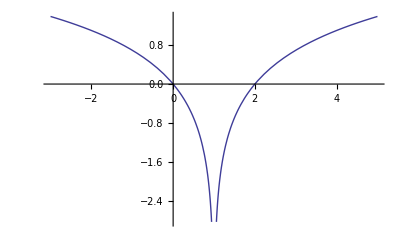

```mathematica
Plot[Re[ {Log[x-1]}],{x,-3,5}]
```

```mathematica
Limit[ Log[x]/x,x->0]
```

-∞

```mathematica
D[Log[x-1],x]
```

1/(-1+x)

```mathematica
ff[x_] := Log[x-1]
```

```mathematica
D[ ff[x],x]
```

1/(-1+x)

```mathematica
FullSimplify[D[ ff[1/x],x]]/.x->3
```

1/6

```mathematica
FullSimplify[D[ff[x],x]/D[ff[x],x]]
```

1/x

```mathematica
D[ff[x],x]/.x->7
```

1/6

```mathematica
D[ff[x],x]/.x->1/7
```

-7/6

```mathematica
Table[ {-(D[ff[x],x]/.x->n)n,D[ff[x],x]/.x->(1/n)},{n,2,8}]
```

{{-2,-2},{-3/2,-3/2},{-4/3,-4/3},{-5/4,-5/4},{-6/5,-6/5},{-7/6,-7/6},{-8/7,-8/7}}

```mathematica
ff[x_] := Log[x]
Table[ {1/(D[ff[x],x]/.x->n),D[ff[x],x]/.x->(1/n)},{n,2,8}]
```

{{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}}

```mathematica
ff[x_] := LogIntegral[x]-Log[Log[x]]-EulerGamma
Table[ {n(D[ff[x],x]/.x->n),D[ff[x],x]/.x->(1/n)},{n,2,8}]
```

{{1/Log[2],1/Log[2]},{2/Log[3],2/Log[3]},{3/Log[4],3/Log[4]},{4/Log[5],4/Log[5]},{5/Log[6],5/Log[6]},{6/Log[7],6/Log[7]},{7/Log[8],7/Log[8]}}

```mathematica
ff[x_] := LogIntegral[x]
Table[ {-(D[ff[x],x]/.x->n),D[ff[x],x]/.x->(1/n)},{n,2,8}]
```

{{-1/Log[2],-1/Log[2]},{-1/Log[3],-1/Log[3]},{-1/Log[4],-1/Log[4]},{-1/Log[5],-1/Log[5]},{-1/Log[6],-1/Log[6]},{-1/Log[7],-1/Log[7]},{-1/Log[8],-1/Log[8]}}

```mathematica
ff[x_] := LogIntegral[x+1]-Log[Log[x+1]]-EulerGamma
Table[ {(D[ff[x],x]/.x->n),D[ff[x],x]/.x->(1/n)},{n,2,8}]
```

{{2/(3 Log[3]),1/(3 Log[3/2])},{3/(4 Log[4]),1/(4 Log[4/3])},{4/(5 Log[5]),1/(5 Log[5/4])},{5/(6 Log[6]),1/(6 Log[6/5])},{6/(7 Log[7]),1/(7 Log[7/6])},{7/(8 Log[8]),1/(8 Log[8/7])},{8/(9 Log[9]),1/(9 Log[9/8])}}

```mathematica
Expand[(D[ff[x],x]/.x->(1/y))-(D[ff[x],x]/.x->y)]
```

1/Log[1+1/y]-1/((1+1/y) Log[1+1/y])-1/Log[1+y]+1/((1+y) Log[1+y])

```mathematica
1/(7 Log[7]-7Log[6])
```

1/(-7 Log[6]+7 Log[7])

```mathematica
(1/x)/(1-(1/x))
```

1/((1-1/x) x)

```mathematica
1/(1-1/x) 1/x
```

1/((1-1/x) x)

```mathematica
x/(x-1) 1/x
```

1/(-1+x)

```mathematica
(g2[100,z]-1)/z/.z->.00001
```

30.1264+6.28508 ⅈ

```mathematica
N@Gamma[0,-Log[4]]
```

-2.96759-3.14159 ⅈ

```mathematica
Integrate[ 1,{s,1,x}, {t,1,x}]
```

(-1+x)^2

```mathematica
Sum[ (-1)^(k+1)/k (x-1)^k,{k,1,Infinity}]
```

Log[x]

```mathematica
d2[100,7]
```

0

```mathematica
D[ Log[x-1],x]
```

1/(-1+x)

```mathematica
D[ LogIntegral[x]-Log[Log[x]]-EulerGamma,x]
```

1/Log[x]-1/(x Log[x])

```mathematica
FullSimplify[D[ LogIntegral[x-1]-Log[Log[x-1]]-EulerGamma,x]]
```

(-2+x)/((-1+x) Log[-1+x])

```mathematica
Limit[Log[x]/(x-1),x->1]
```

1

```mathematica
Limit[ D[ Log[x-1],x],x->1]
```

∞

```mathematica
Limit[ D[LogIntegral[x],x],x->.9999999999]
```

-1.×10^10

```mathematica
D[ g1l[x],x]
```

```mathematica
Integrate[ (1/Log[s]-1/(s Log[s]))(1/Log[t]-1/(t Log[t])),{s,1,x},{t,1,x/s}]
```

∫_1^x -((-1+s) (EulerGamma+Log[Log[x/s]]-LogIntegral[x/s]))/(s Log[s])ⅆs

```mathematica
N[∫_1^x -((-1+s) (EulerGamma+Log[Log[x/s]]-LogIntegral[x/s]))/(s Log[s])ⅆs/.x->100]
```

80.5038

```mathematica
Table[ D[Log[x+1]^2,{x,k}]/k!/.x->0,{k,0,6}]
```

{0,0,1,-1,11/12,-5/6,137/180}

```mathematica
Chop@N@g1lk[100,3,40]
```

134.883

```mathematica
N[Integrate[ D[g1l[s],s]D[g1l[t],t]D[g1l[u],u],{s,1,x},{t,1,x/s}, {u,1,x/(s t)}]/.x->100]
```

134.883

```mathematica
N[D[ g1[100,z],{z,3}]/.z->0]
```

134.883

```mathematica
D[g1l[s],{s,1}]
```

1/Log[s]-1/(s Log[s])

```mathematica
Integrate[ (1/Log[s]-1/(s Log[s]))(1/Log[t]-1/(t Log[t])),{s,1,x},{t,1,x/s}]
```

$Aborted

```mathematica
Table[N[ aa[10,.1^k]],{k,1,5}]
```

{0.840729,0.840946,0.840968,0.84097,0.84097}

```mathematica
N[D[ (LogIntegral[x]-Log[Log[x]]-EulerGamma)^2,x]/.x->10]
```

3.71662

```mathematica
FullSimplify[(1/Log[s]-1/(s Log[s]))(1/Log[t]-1/(t Log[t]))]
```

((-1+s) (-1+t))/(s t Log[s] Log[t])

```mathematica
Integrate[ (1/Log[t]-1/(t Log[t])), t]
```

```mathematica
Limit[ LogIntegral[t]-Log[Log[t]],t->x/s]
```

-Log[Log[x/s]]+LogIntegral[x/s]

```mathematica
Integrate[ (1/Log[s]-1/(s Log[s]))( LogIntegral[x/s]-Log[Log[x/s]]-EulerGamma),{s,1,x}]
```

∫_1^x (1/Log[s]-1/(s Log[s])) (-EulerGamma-Log[Log[x/s]]+LogIntegral[x/s])ⅆs

```mathematica
Integrate[ LogIntegral[x/s],{s,1,x}]
```

$Aborted

```mathematica
Table[ (-1)^(k+1) / k D[g2[n,k],n],{k,1,7}]
```

{1,-Log[n]/2,Log[n]^2/6,-1/24 Log[n]^3,Log[n]^4/120,-1/720 Log[n]^5,Log[n]^6/5040}

```mathematica
Expand[Sum[ (-1)^(k+1) / (k!) Log[n]^(k-1),{k,1,Infinity}]]
```

1/Log[n]-1/(n Log[n])

```mathematica
Table[ (-1)^(k+1) / k D[g2[n,k],{n,2}],{k,1,7}]
```

{0,-1/(2 n),Log[n]/(3 n),-Log[n]^2/(8 n),Log[n]^3/(30 n),-Log[n]^4/(144 n),Log[n]^5/(840 n)}

```mathematica
(-1)^(k+1) / k D[g2[n,k],{n,2}]
```

((-1)^(1+2 k) (-1+k) (-Log[n])^(-2+k))/(k n Gamma[k])

```mathematica
Sum[ ((-1)^(1+2 k) (-1+k) (-Log[n])^(-2+k))/(k n Gamma[k]), {k,1,Infinity}]
```

-(-1+n-Log[n])/(n^2 Log[n]^2)

```mathematica
Integrate[ -(-1+n-Log[n])/(n^2 Log[n]^2), {n,1,x}]
```

ConditionalExpression[-1+(-1+x)/(x Log[x]),Im[x]≠0||Re[x]≥0]

```mathematica
Expand[ -(-1+n-Log[n])/(n^2 Log[n]^2)]
```

1/(n^2 Log[n]^2)-1/(n Log[n]^2)+1/(n^2 Log[n])

```mathematica
Integrate[ D[ Log[s]^2,s]D[Log[t]^2,t],{s,1,x},{t,1,x}]
```

ConditionalExpression[Log[x]^4,Re[x]≥0||x∉Reals]

```mathematica
D[ x^z,{z,3}]/.z->0
```

Log[x]^3

```mathematica
FullSimplify[D[ Log[x]^(a+b),x]]
```

((a+b) Log[x]^(-1+a+b))/x

```mathematica
Sum[ Log[x]^k/(k! k),{k,1,Infinity}]
```

-EulerGamma-Gamma[0,-Log[x]]-Log[-Log[x]]

```mathematica
Limit[ Sum[D[ Log[x]^k,x]/(k! k),{k,1,Infinity}],x->1]
```

1

```mathematica
Limit[Sum[D[ Log[x]^k,{x,2}]/(k! k),{k,1,Infinity}],x->1]
```

-1/2

```mathematica
Limit[ Sum[D[ Log[x]^k,{x,3}]/(k! k),{k,1,Infinity}],x->1]
```

5/6

```mathematica
Limit[ Sum[D[ Log[x]^k,{x,4}]/(k! k),{k,1,Infinity}],x->1]
```

-9/4

```mathematica
Limit[ Sum[D[ Log[x]^k,{x,5}]/(k! k),{k,1,Infinity}],x->1]
```

251/30

```mathematica
Limit[ Sum[D[ Log[x]^k,{x,6}]/(k! k),{k,1,Infinity}],x->1]
```

-475/12

```mathematica
Table[ N[D[ a1[x,z],{z,k}]/.z->0/.x->1],{k,0,8}]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.}

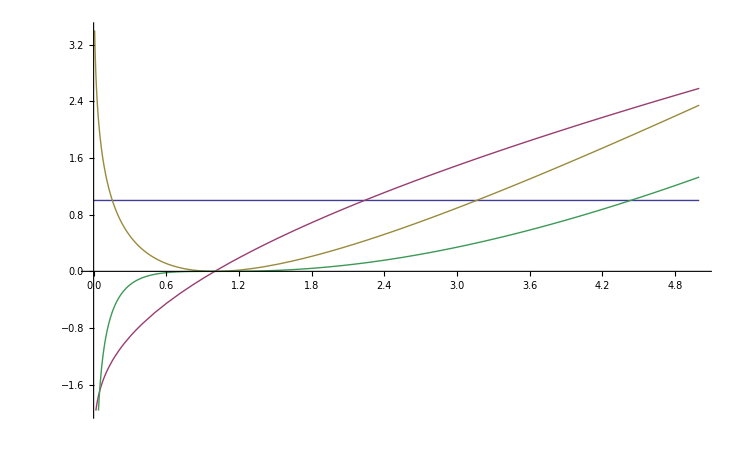

```mathematica
Plot[{1,D[ LaguerreL[-z,Log[x]],{z,1}]/.z->0,  D[ LaguerreL[-z,Log[x]],{z,2}]/.z->0 , D[ LaguerreL[-z,Log[x]],{z,3}]/.z->0},{x,0,5}]
```

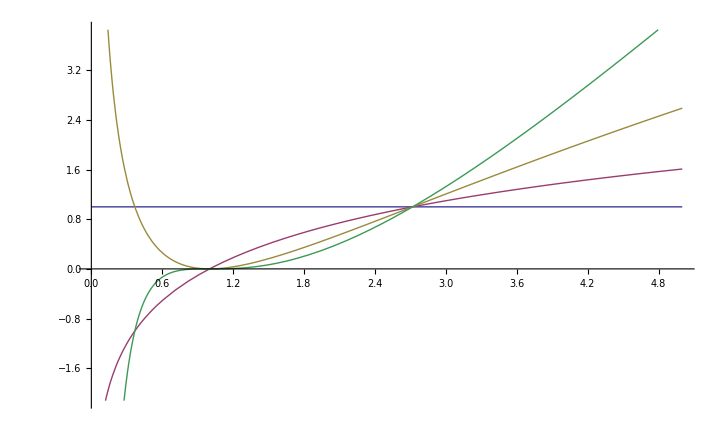

```mathematica
Plot[{1,D[ x^z,{z,1}]/.z->0,  D[ x^z,{z,2}]/.z->0 , D[ x^z,{z,3}]/.z->0},{x,0,5}]
```

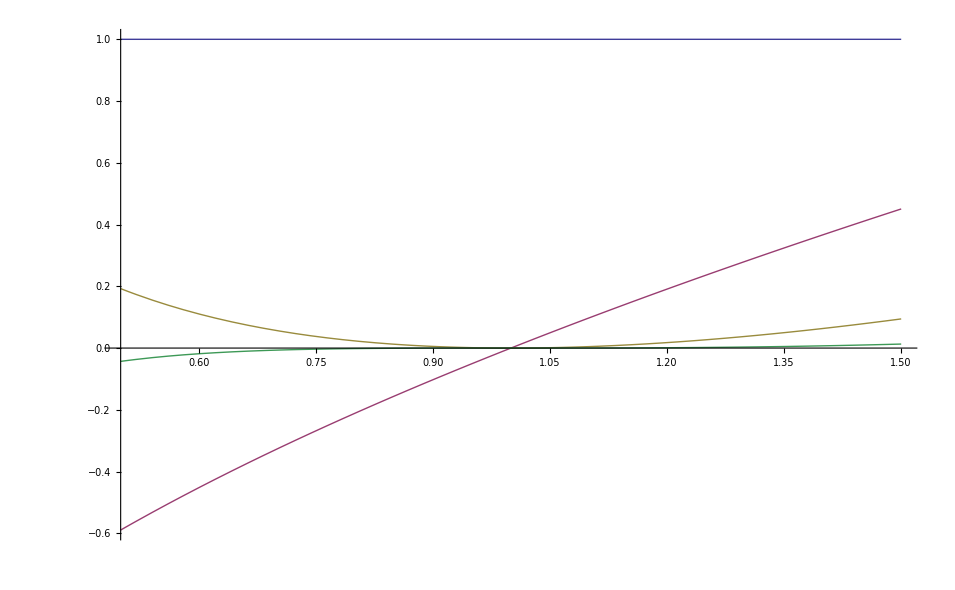

```mathematica
Plot[{1,D[ LaguerreL[-z,Log[x]],{z,1}]/.z->0,  D[ LaguerreL[-z,Log[x]],{z,2}]/.z->0 , D[ LaguerreL[-z,Log[x]],{z,3}]/.z->0},{x,.5,1.5}]
```

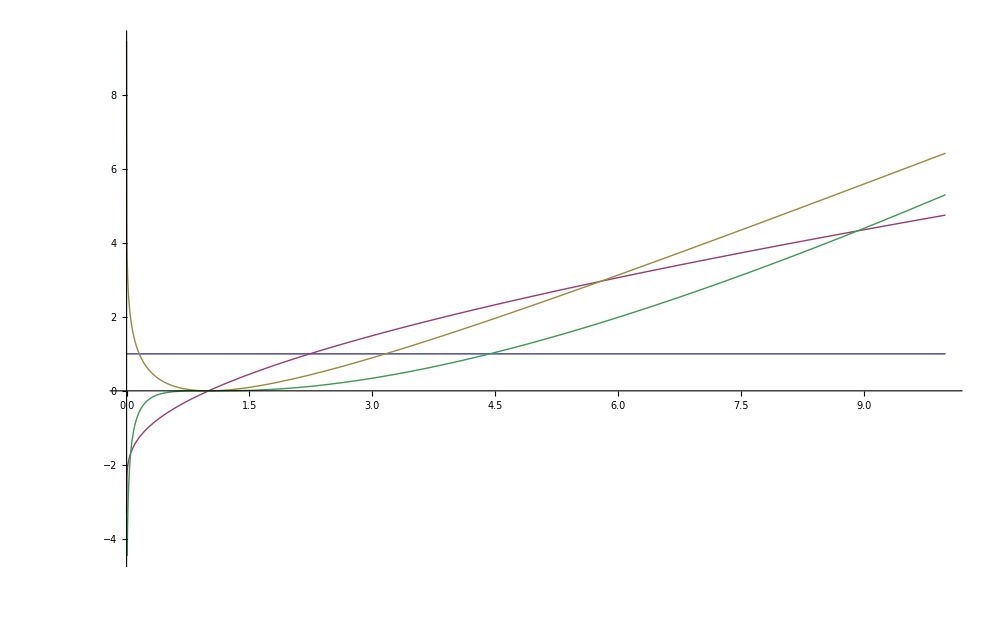

```mathematica
Plot[{1,D[ LaguerreL[-z,Log[x]],{z,1}]/.z->0,  D[ LaguerreL[-z,Log[x]],{z,2}]/.z->0 , D[ LaguerreL[-z,Log[x]],{z,3}]/.z->0},{x,0,10}]
```

```mathematica
ss[x_]:= -ExpIntegralEi[2 Log[x]]+x LogIntegral[x]
```

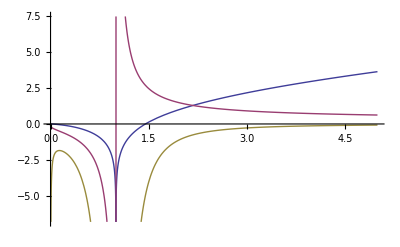

```mathematica
Plot[{LogIntegral[x], 1/Log[x], -1/(x Log[x]^2)},{x,0,5}]
```

```mathematica
FullSimplify[D[ss[x] , {x,4}]]
```

(2+Log[x])/(x^2 Log[x]^3)

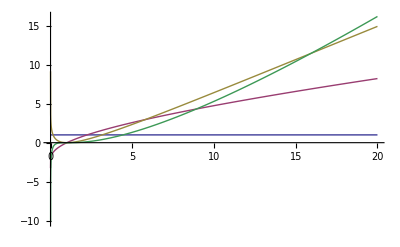

```mathematica
Plot[{1,D[ LaguerreL[-z,Log[x]],{z,1}]/.z->0,  D[ LaguerreL[-z,Log[x]],{z,2}]/.z->0 , D[ LaguerreL[-z,Log[x]],{z,3}]/.z->0},{x,0,20}]
```

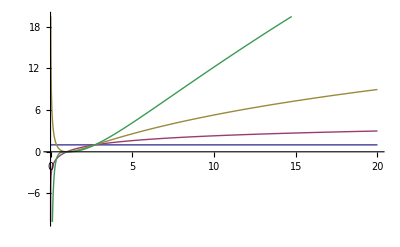

```mathematica
Plot[{1,D[ x^z,{z,1}]/.z->0,  D[ x^z,{z,2}]/.z->0 , D[ x^z,{z,3}]/.z->0},{x,0,20}]
```

```mathematica
D[ Log[x]^(a+b),x]
```

((a+b) Log[x]^(-1+a+b))/x

```mathematica
D[Integrate[ D[ Log[s]^a,s] D[Log[t]^b,t],{s,1,x},{t,1,x}],x]
```

ConditionalExpression[((a+b) Log[x]^(-1+a+b))/x,(Re[x]≥0||x∉Reals)&&Re[a]>0]

```mathematica
FullSimplify[((a+b) Log[x]^(-1+a+b))/x]/.x->100/.a->3/.b->2
```

Log[100]^4/20

```mathematica
D[ Integrate[ D[f[s],s]D[g[t],t],{s,1,x},{t,1,x}],x]
```

-(g[1]-g[x]) f'[x]-(f[1]-f[x]) g'[x]

```mathematica
D[Integrate[ D[ Log[s]^a,s] Integrate[ D[Log[t]^b,t], {t,1,x}],{s,1,x}],x]
```

ConditionalExpression[((a+b) Log[x]^(-1+a+b))/x,(Re[x]≥0||x∉Reals)&&Re[b]>0&&Re[a]>0]

```mathematica
Integrate[ D[Log[t]^b,t], {t,1,x}]
```

ConditionalExpression[Log[x]^b,(Re[x]≥0||x∉Reals)&&Re[b]>0]

```mathematica
D[Integrate[ D[ Log[s]^a,s] Log[x]^b,{s,1,x}],x]
```

ConditionalExpression[((a+b) Log[x]^(-1+a+b))/x,(Re[x]≥0||x∉Reals)&&Re[a]>0]

```mathematica
D[Log[x]^b Integrate[ D[ Log[s]^a,s] ,{s,1,x}],x]
```

ConditionalExpression[((a+b) Log[x]^(-1+a+b))/x,(Re[x]≥0||x∉Reals)&&Re[a]>0]

```mathematica
Integrate[ D[ Log[s]^a,s] ,{s,1,x}]
```

ConditionalExpression[Log[x]^a,(Re[x]≥0||x∉Reals)&&Re[a]>0]

```mathematica
D[Log[x]^b Log[x]^a,x]
```

((a+b) Log[x]^(-1+a+b))/x

```mathematica
D[ Log[s]^a,s] D[Log[t]^b,t]/.{s->x,t->x}
```

(a b Log[x]^(-2+a+b))/x^2

```mathematica
D[ Integrate[ D[f[s],s]D[g[t],t],{s,1,x},{t,1,x/s}],x]
```

∫_1^x (f'[s] g'[x/s])/s ⅆs

```mathematica
ff[x_] := 1/Log[x] - 1/(x Log[x])
```

```mathematica
Sum[ z^k/k! Log[x]^k,{k,0,Infinity}]
```

x^z

```mathematica
Sum[ z^k/k! Log[x]^(k+1),{k,0,Infinity}]
```

x^z Log[x]

```mathematica
D[ x^z, z]
```

x^z Log[x]

```mathematica
Integrate[ D[ Log[s],s] D[ t^z,t],{s,1,x},{t,0,x}]
```

ConditionalExpression[x^z Log[x],Re[x]≥0||x∉Reals]

```mathematica
1+Integrate[ Log[x] x^y,{y,0,z}]
```

x^z

```mathematica
1+Integrate[ D[Log[s],s] Integrate[ x^y,{y,0,z}],{s,1,x}]
```

ConditionalExpression[x^z,Re[x]≥0||x∉Reals]

```mathematica
D[ Log[s],s] D[ t^y,t]
```

(t^(-1+y) y)/s

```mathematica
Integrate[ (t^(-1+y) y)/s, {y,0,z}]
```

(1-t^z+t^z z Log[t])/(s t Log[t]^2)

```mathematica
1+Integrate[D[ Log[s],s] D[ t^y,t],{y,0,z} ,{s,1,x},{t,0,x}]
```

x^z

-1+x^z

```mathematica
1+Integrate[D[ g1l[s],s] D[ g1[t,y],t],{y,0,z} ,{s,1,x},{t,1,x}]
```

1+∫_0^z -(-1+Hypergeometric1F1[y,1,Log[x]]) (EulerGamma+Log[Log[x]]-LogIntegral[x])ⅆy

```mathematica
N[ 1+∫_0^z -(-1+Hypergeometric1F1[y,1,Log[x]]) (EulerGamma+Log[Log[x]]-LogIntegral[x])ⅆy/.{x->100,z->2}]
```

8800.43

```mathematica
N@g1[ 100,2]
```

560.517

```mathematica
Sum[ BernoulliB[k]/(k!) Log[x]^(k+z-1)(x-1),{k,0,Infinity}]
```

Log[x]^z

```mathematica
Sum[ BernoulliB[k]/(k!) Integrate[ D[ Log[y]^(k+z-1),y],{y,1,x}]Integrate[ D[ (y-1),y],{y,1,x}],{k,0,Infinity}]
```

∑_(k=0)^∞ ConditionalExpression[((-1+x) BernoulliB[k] Log[x]^(-1+k+z))/(k!),(Re[x]≥0||x∉Reals)&&Re[k+z]>1]

```mathematica
Integrate[ D[ Log[y]^(k+z-1),y],{y,1,x}]Integrate[ D[ (y-1),y],{y,1,x}]
```

ConditionalExpression[(-1+x) Log[x]^(-1+k+z),(Re[x]≥0||x∉Reals)&&Re[k+z]>1]

```mathematica
Sum[ BernoulliB[k]/(k!)((-1+x) Log[x]^(-1+k+z)),{k,0,Infinity}]
```

Log[x]^z

```mathematica
Integrate[ D[ Log[y]^(k+z-1),y],{y,1,x}]Integrate[ D[ (y-1),y],{y,1,x}]
```

ConditionalExpression[(-1+x) Log[x]^(-1+k+z),(Re[x]≥0||x∉Reals)&&Re[k+z]>1]

```mathematica
1+Integrate[ Log[x] x^y, {y,0,z}]
```

x^z

```mathematica
Integrate[ D[ s^a,s],{s,1,x}]
```

ConditionalExpression[-1+x^a,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ D[ s^a,s]D[t^a,t],{s,1,x},{t,1,x/s}]]
```

ConditionalExpression[1-x^a+a x^a Log[x],Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ D[ s^a,s]D[t^a,t]D[u^a,u],{s,1,x},{t,1,x/s}, {u,1,x/(s t)}]]
```

ConditionalExpression[-1+x^a-a x^a Log[x]+1/2 a^2 x^a Log[x]^2,Re[x]≥0||x∉Reals]

```mathematica
N@((-1)^a Gamma[3,0,-a Log[x]]/Gamma[3])/.{x->100,a->4}
```

-1.5224×10^10+3.72881×10^-6 ⅈ

```mathematica
N[(-1+x^a-a x^a Log[x]+1/2 a^2 x^a Log[x]^2)/.{x->100,a->4}]
```

1.5224×10^10

```mathematica
ffx[ n_, a_, t_] := Sum[ (-1)^(k+1)/k (-1)^k ( 1 - Gamma[ k, -a Log[n]]/Gamma[k]),{k,1, t}]
```

```mathematica
Chop@N[ffx[100,1,30]]
```

28.0217

```mathematica
Chop@N[ffx[100,2,30]]
```

1243.32-1.13248×10^-9 ⅈ

```mathematica
FullSimplify[Integrate[ D[ s^a,s]D[t^a,t],{s,1,x},{t,1,x}]]
```

ConditionalExpression[(-1+x^a)^2,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify[Integrate[ D[ s^a,s]D[t^a,t]D[u^a,u],{s,1,x},{t,1,x}, {u,1,x}]]
```

ConditionalExpression[(-1+x^a)^3,Re[x]≥0||x∉Reals]

```mathematica
Sum[ (-1)^(k+1)/k (x^a-1)^k,{k,1,Infinity}]
```

Log[x^a]

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
```

```mathematica
pp[n_, k_, z_] := Sum[ dz[j,z](1/k-pp[n/j,k+1,z]),{j,2,n}]
```

```mathematica
pp[100,1,3]/3
```

428/15

```mathematica
Limit[ (g1[ 100,a z]-1)/z,z->0]
```

-a LaguerreL^(1,0)[0,Log[100]]

```mathematica
Limit[ (g1[ 100,z]-1)/z,z->0]
```

-LaguerreL^(1,0)[0,Log[100]]

```mathematica
Limit[ (g1[ 100^a,z]-1)/z,z->0]
```

-LaguerreL^(1,0)[0,Log[100^a]]

```mathematica
FullSimplify[Integrate[ D[ s^a,s]D[t^a,t],{s,1,x},{t,1,x}]]
```

ConditionalExpression[(-1+x^a)^2,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify[Integrate[ D[ s,s]D[t,t],{s,1,x^a},{t,1,x^a}]]
```

(-1+x^a)^2

```mathematica
FullSimplify[Integrate[ D[ s^a,s]D[t^a,t],{s,1,x},{t,1,x/s}]]
```

ConditionalExpression[1+x^a (-1+a Log[x]),Re[x]≥0||x∉Reals]

```mathematica
FullSimplify[Integrate[ D[ s,s]D[t,t],{s,1,x^a},{t,1,x^a/s}]]
```

ConditionalExpression[1+x^a (-1+Log[x^a]),Re[x^a]≥0||x^a∉Reals]

```mathematica
Integrate[ D[ s^a,s]D[t^a,t],{s,0,1},{t,0,1}]
```

ConditionalExpression[1,Re[a]>0]

```mathematica
FullSimplify[Integrate[ D[ s^a,s]D[t^a,t],{s,1,x},{t,1,x/s}]]
```

ConditionalExpression[1+x^a (-1+a Log[x]),Re[x]≥0||x∉Reals]

```mathematica
FullSimplify[Integrate[ D[ s^a,s],{s,1,x}]]
```

ConditionalExpression[-1+x^a,Re[x]≥0||x∉Reals]

```mathematica
Expand[1+x^a (-1+a Log[x])+2(-1+x^a)+1]
```

x^a+a x^a Log[x]

```mathematica
N[LaguerreL[ -2, Log[x^a]]/.{x->10,a->2}]
```

560.517

```mathematica
N[x^a+a x^a Log[x]/.{x->10,a->2}]
```

560.517

```mathematica
a1[a1[4,3],2]
```

4096

```mathematica
a1[4,6]
```

4096

```mathematica
N[g1[g1[13,3],2]]
```

711.167

```mathematica
N@g1[13,6]
```

1102.22

```mathematica
N[d1[d1[55,3],2]]
```

4187.

```mathematica
N@d1[55,6]
```

4856.

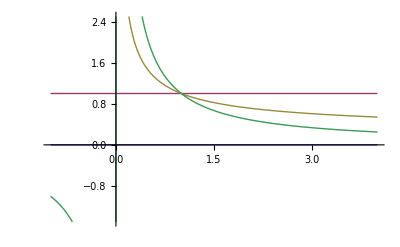

```mathematica
Plot[{0,1,1/Log[x]-1/(x Log[x]),1/x},{x,-1,4}]
```

```mathematica
N@(x D[g1l[x],x])/.x->(1/100)
```

0.214976

```mathematica
FullSimplify[D[g1l[E^x],x]]
```

(-1+ⅇ^x)/Log[ⅇ^x]

```mathematica
(E^x-1)/x
```

(-1+ⅇ^x)/x

```mathematica
Series[(-1+ⅇ^x)/x,{x,0,10}]
```

1+x/2+x^2/6+x^3/24+x^4/120+x^5/720+x^6/5040+x^7/40320+x^8/362880+x^9/3628800+x^10/39916800+O[x]^11

```mathematica
Series[E^x,{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
FullSimplify[D[g1l[x],x]]
```

(-1+x)/(x Log[x])

```mathematica
D[(E^x-1)/x,{x,4}]
```

(24 (-1+ⅇ^x))/x^5-(24 ⅇ^x)/x^4+(12 ⅇ^x)/x^3-(4 ⅇ^x)/x^2+ⅇ^x/x

```mathematica
(-1+ⅇ^x)/x/.x->3
```

1/3 (-1+ⅇ^3)

```mathematica
(-1+ⅇ^x)/x/.x->-3
```

1/3 (1-1/ⅇ^3)

```mathematica
FullSimplify[D[g1l[x],x]]
```

(-1+x)/(x Log[x])

```mathematica
Log[12,31*17]
```

Log[527]/Log[12]

```mathematica
FullSimplify[Log[12,31]+Log[12,17]]
```

Log[527]/Log[12]

```mathematica
N@g1l[g1[1.7,14]]
```

16.2968

```mathematica
Log[ 5,5^7]
```

7

```mathematica
Log[ E^7]
```

7

```mathematica
ff5[ n_, z_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
ff6[ n_, z_] := Integrate[Sum[ z^k / (k!) (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
ff5[n,z]
```

ConditionalExpression[-1+LaguerreL[-z,Log[n]],-1≤Re[Log[n]]≤1||Log[n]∉Reals]

```mathematica
N[ff6[E,N[LogIntegral[6]-Log[Log[6]]-EulerGamma]]]
```

12.0578

```mathematica
Sum[ z^k / (k!) (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}]
```

(ⅇ^-t √z BesselJ[1,2 √t √z])/(√t)

```mathematica
InverseFunction[LogIntegral-]
```

LogIntegral^(-1)

```mathematica
Solve[y==a x+b,x]
```

{{x→(-b+y)/a}}

```mathematica
InverseFunction[Log]
```

Exp

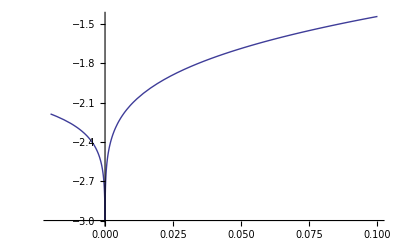

```mathematica
Plot[ Re[LogIntegral[x]-Log[Log[x]]-EulerGamma],{x,-.02,.1}]
```

```mathematica
5 5!
```

600

```mathematica
Sum[ (Log[x])^k / k / k!,{k,1,12}]
```

Log[x]+Log[x]^2/4+Log[x]^3/18+Log[x]^4/96+Log[x]^5/600+Log[x]^6/4320+Log[x]^7/35280+Log[x]^8/322560+Log[x]^9/3265920+Log[x]^10/36288000+Log[x]^11/439084800+Log[x]^12/5748019200

```mathematica
Expand[1/4(Log[x]+Log[x]^2/4+Log[x]^3/18+Log[x]^4/96+Log[x]^5/600+Log[x]^6/4320+Log[x]^7/35280+Log[x]^8/322560)^2]
```

Log[x]^2/4+Log[x]^3/8+(25 Log[x]^4)/576+(7 Log[x]^5)/576+(1507 Log[x]^6)/518400+(53 Log[x]^7)/86400+(15787 Log[x]^8)/135475200+(12317 Log[x]^9)/609638400+(6943 Log[x]^10)/2257920000+(289 Log[x]^11)/677376000+(15557 Log[x]^12)/292626432000+(143 Log[x]^13)/24385536000+(107 Log[x]^14)/191182602240+Log[x]^15/22759833600+Log[x]^16/416179814400

```mathematica
f1[x] := Log[x]+Log[x]^2/4+Log[x]^3/18+Log[x]^4/96+Log[x]^5/600+Log[x]^6/4320+Log[x]^7/35280+Log[x]^8/322560+Log[x]^9/3265920+Log[x]^10/36288000+Log[x]^11/439084800+Log[x]^12/5748019200
```

```mathematica
f1[x]-Expand[(1/4)f1[x]^2]+Expand[(5/72) f1[x]^3 ]-Expand[(11/576) f1[x]^4 ]+Expand[(431/86400) f1[x]^5 ]
```

```mathematica
2!3!3!
```

72

```mathematica
2! 3! 4! 5! 6! 6!
```

17915904000

```mathematica
17915904000/1036800
```

17280

```mathematica
4147200/86400
```

48

```mathematica
1241 17280
```

21444480

```mathematica
Sum[ (x)^k / k / k!,{k,1,12}]
```

x+x^2/4+x^3/18+x^4/96+x^5/600+x^6/4320+x^7/35280+x^8/322560+x^9/3265920+x^10/36288000+x^11/439084800+x^12/5748019200

```mathematica
f1[x] := x+x^2/4+x^3/18+x^4/96+x^5/600+x^6/4320+x^7/35280+x^8/322560+x^9/3265920+x^10/36288000+x^11/439084800+x^12/5748019200
```

```mathematica
Expand[f1[x]-(1/4)f1[x]^2+(5/72) f1[x]^3 -(132/6912) f1[x]^4+(20688/4147200) f1[x]^5 -(21444480/17915904000) f1[x]^6 ]
```

x-(3055 x^7)/12192768-(215867 x^8)/541900800-(458392747 x^9)/1316818944000-(413541517 x^10)/1881169920000-(85420232869 x^11)/764808442675200-(1055410491367 x^12)/21851669790720000-(126628969850413 x^13)/6883275984076800000-(51622810392787 x^14)/8176497532600320000-(24088066977405451 x^15)/12142098835911475200000-(50999322463996549 x^16)/88306173352083456000000-(763389979133343253 x^17)/4856839534364590080000000-(10563123451990645139 x^18)/262269334855687864320000000-(3417320410902077653 x^19)/349692446474250485760000000-(500817403129821473 x^20)/222026950142381260800000000-(15335389813412775362791 x^21)/30842873779028892844032000000000-(62699227636446189380059 x^22)/597118036361999365460459520000000-(4543102502230399150537 x^23)/213256441557856916235878400000000-(182587187718254540072359 x^24)/43869896549044851339952128000000000-(3904078316405013432934841 x^25)/4975983636349994712170496000000000000-(25609439445175101986598157 x^26)/179135410908599809638137856000000000000-(4356022931635351618763647 x^27)/172737717661864102151061504000000000000-(8175273442776233537431984091 x^28)/1895969189056620385210051067904000000000000-(226104426237460056487870213 x^29)/315994864842770064201675177984000000000000-(8946884706021209379035991601 x^30)/77562375915952652122229361868800000000000000-(192836206394489566938536011 x^31)/10664826688443489666806537256960000000000000-(5020113801081632634102991411 x^32)/1820130421494355569801649025187840000000000000-(152257060374299562476061868241 x^33)/371647880438878727908874210330542080000000000000-(654121679169499461313234447 x^34)/11032219085384155188389586948587520000000000000-(121870630710376604408981410174609 x^35)/14568596913204046134027869044957249536000000000000000-(724421904025071453646974034026683 x^36)/629363386650414792990003942742153179955200000000000000-(32415927097725954050829815301659 x^37)/209787795550138264330001314247384393318400000000000000-(125828531086844128226335327073 x^38)/6215934682967059683851890792515093135360000000000000-(1955038084336375700912177321791 x^39)/755236063980497751588004731290583815946240000000000000-(195264123788589015093036780574229 x^40)/604188851184398201270403785032467052756992000000000000000-(2380251621154507632525466292783 x^41)/60418885118439820127040378503246705275699200000000000000-(499763701860048526410311037779303 x^42)/106578913348927842704099227679727188106333388800000000000000-(276582759193593821849926593983 x^43)/507518634994894489067139179427272324315873280000000000000-(5523584363578214753721695121043 x^44)/89323279759101430075816495579199929079593697280000000000000-(5678767436702113736893011494405371 x^45)/829031690264160147891171849594449341769979002880000000000000000-(98232593461144257000053568519703 x^46)/132645070442265623662587495935111894683196640460800000000000000-(1036271840620076511517774653289 x^47)/13264507044226562366258749593511189468319664046080000000000000-(438704872317370827448425003069271 x^48)/54573971839103570878321712613303179526800903503872000000000000000-(916931542353162104672307470971 x^49)/1136957746647991059965035679443816240141685489664000000000000000-(256125784743372048563096893937 x^50)/3248450704708545885614387655553760686119101399040000000000000000-(349172362032207523755321064457 x^51)/46511907817417816089478732340883391642159860940800000000000000000-(1898160047118482821933365139811 x^52)/2728698591955178543916085630665158976340045175193600000000000000000-(3054109987346644108351072453 x^53)/48726760570628188284215814833306410291786520985600000000000000000-(37119794770101712227937667629 x^54)/6766058753521514144608253145424832971945214056857600000000000000000-(1236244591274859992631178031053 x^55)/2653172113070704852075551117673534040387776067665920000000000000000000-(651164395582185202142914533571 x^56)/16980301523652511053283527153110617858481766833061888000000000000000000-(14583044165939892912814395163 x^57)/4775709803527268733735992011812361272697996921798656000000000000000000-(10171750897721203243416251 x^58)/43317095723603344523682467227323004741024915390464000000000000000000-(2638198025861236550540413 x^59)/151609835032611705832888635295630516593587203866624000000000000000000-(676466006722995785415016477 x^60)/545795406117402140998399087064269859736913933919846400000000000000000000-(128238193726920880332277 x^61)/1516098350326117058328886352956305165935872038666240000000000000000000-(33414749902373535304177 x^62)/6064393401304468233315545411825220663743488154664960000000000000000000-(159528956762588769877 x^63)/467824633814916120855770646055088451203069086217011200000000000000000-(22102088800050784183 x^64)/1108917650524245619806271161019468921370237833995878400000000000000000-(15134883208270559 x^65)/13861470631553070247578389512743361517127972924948480000000000000000-(3350943683257699327 x^66)/60380566071045173998451464717510082768609450061075578880000000000000000-(157417411200169 x^67)/60990470778833509089344913856070790675363080869773312000000000000000-(1364276456267 x^68)/12673344577419949940643098983079644815659860959952896000000000000000-(1012021849 x^69)/259227502719953521513154297381174553047588065089945600000000000000-(6119371 x^70)/52369192468677479093566524723469606676280417189888000000000000000-(1241 x^71)/476083567897067991759695679304269151602549247180800000000000000-(1241 x^72)/37394200242096976807307006083535322453145686324019200000000000000

```mathematica
Product[ k!,{k,1,n}]
```

BarnesG[2+n]

```mathematica
f1[ x_] := ExpIntegralEi[ x]-Log[x]-EulerGamma
f2[x_] := f1[x]-(1/4)f1[x]^2+(5/72) f1[x]^3 -(132/6912) f1[x]^4+(20688/4147200) f1[x]^5 -(21444480/17915904000) f1[x]^6
```

```mathematica
N[f2[.2]]
```

0.2

```mathematica
N@g1[2,3]
```

5.25304

```mathematica
{N@g1[ 7,g1[2,3]],N@g1[g1[ 7,3],2],N@g1[g1[ 7,2],3], N@g1[7,g1m[3,2]]}
```

{208.207,230.86,239.868,150.828}

```mathematica
{N@a1[ 7,2 3],N@a1[a1[ 7,3],2],N@a1[a1[ 7,2],3]}
```

{117649.,117649.,117649.}

```mathematica
g1m[N@FullSimplify[g1m[5,5]],5]x
```

26.5505

```mathematica
N@FullSimplify[g1m[3,2]]
```

6.70951

```mathematica
N@g1[5,3]
```

27.5701

```mathematica
N[g1[107,4]]
```

6931.13

```mathematica
N[(x/6 Log[x]^3 - x/2 Log[x]^2 + x Log[x] - x + 1)+4(x/2 Log[x]^2 - x Log[x] + x - 1) + 6(x Log[x]-x+1) + 4 (x-1) + 1 /.x->107]
```

6931.13

```mathematica
g1[x_,1]:=1
g1[ x_, 2] := x (1+Log[x])
g1[ x_, 3] := 1/2 x (2+Log[x] (4+Log[x]))
g1[x_, 4] := 1/6 x (6+Log[x] (3+Log[x]) (6+Log[x]))
g1[x_, 5] := 1/24 x (24+Log[x] (4+Log[x]) (24+Log[x] (12+Log[x])))
```

```mathematica
FullSimplify[(x Log[x]-x+1) + 2 (x-1) + 1]
```

x (1+Log[x])

```mathematica
FullSimplify[(x/2 Log[x]^2 - x Log[x] + x - 1) + 3(x Log[x]-x+1) + 3 (x-1) + 1]
```

1/2 x (2+Log[x] (4+Log[x]))

```mathematica
FullSimplify[(x/6 Log[x]^3 - x/2 Log[x]^2 + x Log[x] - x + 1)+4(x/2 Log[x]^2 - x Log[x] + x - 1) + 6(x Log[x]-x+1) + 4 (x-1) + 1]
```

1/6 x (6+Log[x] (3+Log[x]) (6+Log[x]))

```mathematica
FullSimplify[(x/24Log[x]^4-x/6 Log[x]^3 + x/2 Log[x]^2 - x Log[x] + x - 1)+5(x/6 Log[x]^3 - x/2 Log[x]^2 + x Log[x] - x + 1)+10(x/2 Log[x]^2 - x Log[x] + x - 1) + 10(x Log[x]-x+1) + 5 (x-1) + 1]
```

1/24 x (24+Log[x] (4+Log[x]) (24+Log[x] (12+Log[x])))

```mathematica
N[1/24 x (24+Log[x] (4+Log[x]) (24+Log[x] (12+Log[x])))/.x->107]
```

18520.1

```mathematica
Expand[D[ g1[x,5],x]]
```

5+10 Log[x]+5 Log[x]^2+(5 Log[x]^3)/6+Log[x]^4/24

```mathematica
N[Integrate[ 5+10 Log[x]+5 Log[x]^2+(5 Log[x]^3)/6+Log[x]^4/24,{x,0,y}]/.y->120]
```

22074.2

```mathematica
N@g1[120,6]
```

54338.7

```mathematica
g1a[x_, z_] := Sum[ Binomial[z,k]/((k-1)!)Integrate[ Log[y]^(k-1),{y,0,x}],{k,1,z}]
g1b[x_, z_] := Integrate[Sum[ Binomial[z,k]/((k-1)!) Log[y]^(k-1),{k,1,z}],{y,0,x}]
g1d[x_, z_] :=Sum[ Binomial[z,k]/((k-1)!) Log[x]^(k-1),{k,1,z}]
```

```mathematica
FullSimplify[Expand[g1a[x,6]]]
```

1/120 x (120+Log[x] (20+Log[x] (10+Log[x])) (30+Log[x] (15+Log[x])))

```mathematica
Table[ Binomial[5,k]/((k-1)!),{k,1,5}]
```

{5,10,5,5/6,1/24}

```mathematica
Integrate[ Log[y]^(k-1),{y,0,x}]
```

ConditionalExpression[-(-1)^k Gamma[k]+(Gamma[k]-Gamma[k,-Log[x]]) (-Log[x])^-k Log[x]^k,Im[Log[x]]≠0||Log[x]<0]

```mathematica
N@g1b[120,6]
```

54338.7

```mathematica
Sum[ Binomial[z,k]/((k-1)!) Log[y]^(k-1),{k,1,z}]
```

z Hypergeometric1F1[1-z,2,-Log[y]]

```mathematica
g1d[x,k]
```

(x Gamma[k,Log[x]])/Gamma[k]

```mathematica
Expand[D[ g1[x,3],x]]
```

3+3 Log[x]+Log[x]^2/2

```mathematica
Expand[Integrate[ g1d[y,1]g1d[s,1],{y,1,x}, {s,1,x/y}]]
```

ConditionalExpression[1-x+x Log[x],Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,1]g1d[s,1]g1d[t,1]g1d[u,1],{y,1,x}, {s,1,x/y}, {t,1,x/(y s)}, {u,1,x/(y s t)}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2],{y,1,x}, {s,1,x/y}]]
```

ConditionalExpression[1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3,Re[x]≥0||x∉Reals]

```mathematica
Integrate[ g1d[y,2],{y,1,x}]
```

```mathematica
Expand[g1d[y,2]]
```

2+Log[y]

```mathematica
Expand[Integrate[ 4+2 Log[s]+2 Log[y]+Log[s] Log[y],{y,1,x}, {s,1,x/y}]]
```

ConditionalExpression[1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[g1d[y,2],{y,1,x}]]
```

ConditionalExpression[-1+x+x Log[x],Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ 2+Log[y],{y,1,x}]]
```

ConditionalExpression[-1+x+x Log[x],Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2+7/6 x Log[x]^3+5/24 x Log[x]^4+1/120 x Log[x]^5,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2]g1d[u,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)},{u,1,x/(y s t)}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3+5/8 x Log[x]^4+17/120 x Log[x]^5+7/720 x Log[x]^6+(x Log[x]^7)/5040,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2]g1d[u,2]g1d[v,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)},{u,1,x/(y s t)}, {v,1,x/(y s t u)}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4+31/120 x Log[x]^5+49/720 x Log[x]^6+(31 x Log[x]^7)/5040+(x Log[x]^8)/4480+(x Log[x]^9)/362880,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2]g1d[u,2]g1d[v,2]g1d[w,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)},{u,1,x/(y s t)}, {v,1,x/(y s t u)},{w,1,x/(y s t u v)}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5+7/80 x Log[x]^6+(43 x Log[x]^7)/1680+(37 x Log[x]^8)/13440+(7 x Log[x]^9)/51840+(11 x Log[x]^10)/3628800+(x Log[x]^11)/39916800,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2]g1d[u,2]g1d[v,2]g1d[w,2]g1d[r,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)},{u,1,x/(y s t)}, {v,1,x/(y s t u)},{w,1,x/(y s t u v)},{r,1,x/(y s t u v w)}]]
```

$Aborted

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2]g1d[u,2]g1d[v,2]g1d[w,2]g1d[r,2]g1d[p,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)},{u,1,x/(y s t)}, {v,1,x/(y s t u)},{w,1,x/(y s t u v)},{r,1,x/(y s t u v w)}, {p,1,x/(y s t u v w r)}]]

FullSimplify[-1+x-x Log[x]+1/2 x Log[x]^2+7/6 x Log[x]^3+5/24 x Log[x]^4+1/120 x Log[x]^5]
```

-1+x+1/120 x Log[x] (-120+Log[x] (60+Log[x] (140+Log[x] (25+Log[x]))))

```mathematica
FullSimplify[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3+5/8 x Log[x]^4+17/120 x Log[x]^5+7/720 x Log[x]^6+(x Log[x]^7)/5040]
```

1-x+(x Log[x] (5040+Log[x] (-2520+Log[x] (840+Log[x] (3150+Log[x] (714+Log[x] (49+Log[x])))))))/5040

```mathematica
Table[Log[x]^k Binomial[7,k]/k!,{k,0,7}]
```

{1,7 Log[x],(21 Log[x]^2)/2,(35 Log[x]^3)/6,(35 Log[x]^4)/24,(7 Log[x]^5)/40,(7 Log[x]^6)/720,Log[x]^7/5040}

```mathematica
Expand[(x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3+5/8 x Log[x]^4+17/120 x Log[x]^5+7/720 x Log[x]^6+(x Log[x]^7)/5040)/x]
```

1+Log[x]-Log[x]^2/2+Log[x]^3/6+(5 Log[x]^4)/8+(17 Log[x]^5)/120+(7 Log[x]^6)/720+Log[x]^7/5040

```mathematica
1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3
```

1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3

```mathematica
aa[k_] := (-1)^(k+1) + Sum[ (-1)^(k-j) Binomial[k,j] x Log[x]^j/j!,{j,0,k}]
bb[k_] := (-1)^(k+1) + Sum[ (-1)^(k-j) x Log[x]^j/j!,{j,0,k}]
```

```mathematica
(1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3)-bb[3]
```

2 x Log[x]^2

```mathematica
(-1+x-x Log[x]+1/2 x Log[x]^2+7/6 x Log[x]^3+5/24 x Log[x]^4+1/120 x Log[x]^5)-bb[5]
```

-2+2 x-2 x Log[x]+x Log[x]^2+x Log[x]^3+1/4 x Log[x]^4

```mathematica
(1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3+5/8 x Log[x]^4+17/120 x Log[x]^5+7/720 x Log[x]^6+(x Log[x]^7)/5040)-bb[7]
```

2/3 x Log[x]^4+2/15 x Log[x]^5+1/90 x Log[x]^6

```mathematica
ff1[x_] := -1+x+x Log[x]
ff2[ x_] :=1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3
ff3[x_] := -1+x-x Log[x]+1/2 x Log[x]^2+7/6 x Log[x]^3+5/24 x Log[x]^4+1/120 x Log[x]^5
ff4[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3+5/8 x Log[x]^4+17/120 x Log[x]^5+7/720 x Log[x]^6+(x Log[x]^7)/5040
ff5[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4+31/120 x Log[x]^5+49/720 x Log[x]^6+(31 x Log[x]^7)/5040+(x Log[x]^8)/4480+(x Log[x]^9)/362880
ff6[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5+7/80 x Log[x]^6+(43 x Log[x]^7)/1680+(37 x Log[x]^8)/13440+(7 x Log[x]^9)/51840+(11 x Log[x]^10)/3628800+(x Log[x]^11)/39916800
ff7[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6+(127 x Log[x]^7)/5040+(107 x Log[x]^8)/13440+(13 x Log[x]^9)/13440+(209 x Log[x]^10)/3628800+(71 x Log[x]^11)/39916800+(13 x Log[x]^12)/479001600+(x Log[x]^13)/6227020800
ff8[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040+(17 x Log[x]^8)/2688+(769 x Log[x]^9)/362880+(341 x Log[x]^10)/1209600+(769 x Log[x]^11)/39916800+(13 x Log[x]^12)/17740800+(97 x Log[x]^13)/6227020800+(x Log[x]^14)/5811886080+(x Log[x]^15)/1307674368000
ff9[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320+(73 x Log[x]^9)/51840+(1793 x Log[x]^10)/3628800+(563 x Log[x]^11)/7983360+(2561 x Log[x]^12)/479001600+(1471 x Log[x]^13)/6227020800+(109 x Log[x]^14)/17435658240+(127 x Log[x]^15)/1307674368000+(17 x Log[x]^16)/20922789888000+(x Log[x]^17)/355687428096000
ff10[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880+(341 x Log[x]^10)/1209600+(4097 x Log[x]^11)/39916800+(7423 x Log[x]^12)/479001600+(7937 x Log[x]^13)/6227020800+(5503 x Log[x]^14)/87178291200+(197 x Log[x]^15)/100590336000+(799 x Log[x]^16)/20922789888000+(23 x Log[x]^17)/50812489728000+(19 x Log[x]^18)/6402373705728000+(x Log[x]^19)/121645100408832000
ff11[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800+(2047 x Log[x]^11)/39916800+(9217 x Log[x]^12)/479001600+(18943 x Log[x]^13)/6227020800+(23297 x Log[x]^14)/87178291200+(18943 x Log[x]^15)/1307674368000+(85 x Log[x]^16)/167382319104+(4159 x Log[x]^17)/355687428096000+(1121 x Log[x]^18)/6402373705728000+(199 x Log[x]^19)/121645100408832000+(x Log[x]^20)/115852476579840000+(x Log[x]^21)/51090942171709440000
ff12[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800+(13 x Log[x]^12)/1520640+(6827 x Log[x]^13)/2075673600+(2243 x Log[x]^14)/4151347200+(65537 x Log[x]^15)/1307674368000+(61183 x Log[x]^16)/20922789888000+(40193 x Log[x]^17)/355687428096000+(18943 x Log[x]^18)/6402373705728000+(6401 x Log[x]^19)/121645100408832000+(31 x Log[x]^20)/49651061391360000+(241 x Log[x]^21)/51090942171709440000+(23 x Log[x]^22)/1124000727777607680000+(x Log[x]^23)/25852016738884976640000
ff13[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600+(8191 x Log[x]^13)/6227020800+(15019 x Log[x]^14)/29059430400+(12743 x Log[x]^15)/145297152000+(178177 x Log[x]^16)/20922789888000+(187903 x Log[x]^17)/355687428096000+(141569 x Log[x]^18)/6402373705728000+(78079 x Log[x]^19)/121645100408832000+(907 x Log[x]^20)/69511485947904000+(9439 x Log[x]^21)/51090942171709440000+(667 x Log[x]^22)/374666909259202560000+(41 x Log[x]^23)/3693145248412139520000+(x Log[x]^24)/24817936069329577574400+(x Log[x]^25)/15511210043330985984000000
ff14[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800-(x Log[x]^12)/479001600+(x Log[x]^13)/6227020800+(5461 x Log[x]^14)/29059430400+(19661 x Log[x]^15)/261534873600+(91477 x Log[x]^16)/6974263296000+(471041 x Log[x]^17)/355687428096000+(184661 x Log[x]^18)/2134124568576000+(471041 x Log[x]^19)/121645100408832000+(297727 x Log[x]^20)/2432902008176640000+(7451 x Log[x]^21)/2688996956405760000+(50623 x Log[x]^22)/1124000727777607680000+(13441 x Log[x]^23)/25852016738884976640000+(103 x Log[x]^24)/24817936069329577574400+(337 x Log[x]^25)/15511210043330985984000000+(x Log[x]^26)/14936720782466875392000000+(x Log[x]^27)/10888869450418352160768000000
ff15[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600-(x Log[x]^13)/6227020800+(x Log[x]^14)/87178291200+(4681 x Log[x]^15)/186810624000+(19363 x Log[x]^16)/1902071808000+(647167 x Log[x]^17)/355687428096000+(1216513 x Log[x]^18)/6402373705728000+(1579007 x Log[x]^19)/121645100408832000+(299213 x Log[x]^20)/486580401635328000+(12547 x Log[x]^21)/601069907902464000+(116173 x Log[x]^22)/224800145555521536000+(48563 x Log[x]^23)/5170403347776995328000+(5167 x Log[x]^24)/41363226782215962624000+(6197 x Log[x]^25)/5170403347776995328000000+(19 x Log[x]^26)/2358429597231611904000000+(x Log[x]^27)/27848770972936962048000000+(29 x Log[x]^28)/304888344611713860501504000000+(x Log[x]^29)/8841761993739701954543616000000
ff16[x_] := 1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800-(x Log[x]^12)/479001600+(x Log[x]^13)/6227020800-(x Log[x]^14)/87178291200+(x Log[x]^15)/1307674368000+(4369 x Log[x]^16)/1394852659200+(458753 x Log[x]^17)/355687428096000+(1507327 x Log[x]^18)/6402373705728000+(1026731 x Log[x]^19)/40548366802944000+(4374527 x Log[x]^20)/2432902008176640000+(4571137 x Log[x]^21)/51090942171709440000+(241937 x Log[x]^22)/74933381851840512000+(4691 x Log[x]^23)/54425298397652582400+(12547 x Log[x]^24)/7299392961567522816000+(15913 x Log[x]^25)/620448401733239439360000+(12743 x Log[x]^26)/44810162347400626176000000+(8363 x Log[x]^27)/3629623150139450720256000000+(4031 x Log[x]^28)/304888344611713860501504000000+(449 x Log[x]^29)/8841761993739701954543616000000+(31 x Log[x]^30)/265252859812191058636308480000000+(x Log[x]^31)/8222838654177922817725562880000000
ff17[x_] := -1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600-(x Log[x]^13)/6227020800+(x Log[x]^14)/87178291200-(x Log[x]^15)/1307674368000+(x Log[x]^16)/20922789888000+(131071 x Log[x]^17)/355687428096000+(983041 x Log[x]^18)/6402373705728000+(496201 x Log[x]^19)/17377871486976000+(7667713 x Log[x]^20)/2432902008176640000+(11829247 x Log[x]^21)/51090942171709440000+(13516801 x Log[x]^22)/1124000727777607680000+(11829247 x Log[x]^23)/25852016738884976640000+(1617101 x Log[x]^24)/124089680346647887872000+(872243 x Log[x]^25)/3102242008666197196800000+(41381 x Log[x]^26)/8962032469480125235200000+(627199 x Log[x]^27)/10888869450418352160768000000+(10991 x Log[x]^28)/20325889640780924033433600000+(33151 x Log[x]^29)/8841761993739701954543616000000+(1643 x Log[x]^30)/88417619937397019545436160000000+(73 x Log[x]^31)/1174691236311131831103651840000000+(x Log[x]^32)/7973661725263440308097515520000000+(x Log[x]^33)/8683317618811886495518194401280000000
xx[x_, z_] := 0
xx[x_, 1]:= ff1[x];xx[x_, 2]:= ff2[x];xx[x_, 3]:= ff3[x];xx[x_, 4]:= ff4[x];xx[x_, 5]:= ff5[x];xx[x_, 6]:= ff6[x];xx[x_, 7]:= ff7[x];xx[x_, 8]:= ff8[x];xx[x_, 9]:= ff9[x];xx[x_, 10]:= ff10[x];xx[x_, 11]:= ff11[x];xx[x_, 12]:= ff12[x];xx[x_, 13]:= ff13[x];xx[x_, 14]:= ff14[x];xx[x_, 15]:= ff15[x];xx[x_, 16]:= ff16[x];xx[x_, 17]:= ff17[x]
```

```mathematica
N@xx[10,0]
```

0.

```mathematica
N@Sum[ (-1)^(k+1)/k xx[8,k],{k,1,17}]
```

7.88882

```mathematica
2N[LogIntegral[8]-Log[Log[8]]-EulerGamma]
```

7.88881

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2],{y,1,x}, {s,1,x/y}]]
```

ConditionalExpression[1-x+x Log[x]+3/2 x Log[x]^2+1/6 x Log[x]^3,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]g1d[s,2]g1d[t,2],{y,1,x}, {s,1,x/y},{t,1,x/(y s)}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2+7/6 x Log[x]^3+5/24 x Log[x]^4+1/120 x Log[x]^5,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ g1d[y,2]Integrate[ g1d[s,2]g1d[t,2], {s,1,x/y},{t,1,x/(y s)}],{y,1,x}]]
```

Integrate::pwrl: Unable to prove that integration limits {x} are real. Adding assumptions may help.

∫_1^x ConditionalExpression[((y+1/6 x (-6+Log[x/y] (6+Log[x/y] (9+Log[x/y])))) (2+Log[y]))/y,(x/y∉Reals||(Re[x/y]≥0&&(Re[x/y]≤1||x y≠y^2)))&&((Im[x]≠(Im[y] Re[x])/Re[y]&&Re[y]≠0)||(Re[x]≥0&&Re[y]>0)||(Re[x]≤0&&Re[y]<0)||(Re[y]==0&&((y∉Reals&&Re[x]≠0)||(Re[x]==0&&((Im[x]≥0&&Im[y]>0)||(Im[x]≤0&&Im[y]<0))))))]ⅆy

```mathematica
Expand[Integrate[ g1d[s,2]g1d[t,2], {s,1,x/y},{t,1,x/(y s)}]]
```

ConditionalExpression[1-x/y+(x Log[x/y])/y+(3 x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y),(x/y∉Reals||(Re[x/y]≥0&&(Re[x/y]≤1||x y≠y^2)))&&((Im[x]≠(Im[y] Re[x])/Re[y]&&Re[y]≠0)||(Re[x]≥0&&Re[y]>0)||(Re[x]≤0&&Re[y]<0)||(Re[y]==0&&((y∉Reals&&Re[x]≠0)||(Re[x]==0&&((Im[x]≥0&&Im[y]>0)||(Im[x]≤0&&Im[y]<0))))))]

```mathematica
Expand[Integrate[g1d[y,2](1-x/y+(x Log[x/y])/y+(3 x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)),{y,1,x}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2+7/6 x Log[x]^3+5/24 x Log[x]^4+1/120 x Log[x]^5,Re[x]≥0||x∉Reals]

```mathematica
1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5+7/80 x Log[x]^6+(43 x Log[x]^7)/1680+(37 x Log[x]^8)/13440+(7 x Log[x]^9)/51840+(11 x Log[x]^10)/3628800+(x Log[x]^11)/39916800/.x->x/y
```

```mathematica
Integrate[ g1d[y,2](1-x/y+(x Log[x/y])/y-(x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)-(x Log[x/y]^4)/(24 y)+(x Log[x/y]^5)/(120 y)+(7 x Log[x/y]^6)/(80 y)+(43 x Log[x/y]^7)/(1680 y)+(37 x Log[x/y]^8)/(13440 y)+(7 x Log[x/y]^9)/(51840 y)+(11 x Log[x/y]^10)/(3628800 y)+(x Log[x/y]^11)/(39916800 y)),{y,1,x}]
```

ConditionalExpression[1/6227020800(-6227020800+6227020800 x-6227020800 x Log[x]+3113510400 x Log[x]^2-1037836800 x Log[x]^3+259459200 x Log[x]^4-51891840 x Log[x]^5+8648640 x Log[x]^6+156911040 x Log[x]^7+49575240 x Log[x]^8+6023160 x Log[x]^9+358644 x Log[x]^10+11076 x Log[x]^11+169 x Log[x]^12+x Log[x]^13),Re[x]≥0||x∉Reals]

```mathematica
Expand[1/6227020800(-6227020800+6227020800 x-6227020800 x Log[x]+3113510400 x Log[x]^2-1037836800 x Log[x]^3+259459200 x Log[x]^4-51891840 x Log[x]^5+8648640 x Log[x]^6+156911040 x Log[x]^7+49575240 x Log[x]^8+6023160 x Log[x]^9+358644 x Log[x]^10+11076 x Log[x]^11+169 x Log[x]^12+x Log[x]^13)]
```

-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6+(127 x Log[x]^7)/5040+(107 x Log[x]^8)/13440+(13 x Log[x]^9)/13440+(209 x Log[x]^10)/3628800+(71 x Log[x]^11)/39916800+(13 x Log[x]^12)/479001600+(x Log[x]^13)/6227020800

```mathematica
-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6+(127 x Log[x]^7)/5040+(107 x Log[x]^8)/13440+(13 x Log[x]^9)/13440+(209 x Log[x]^10)/3628800+(71 x Log[x]^11)/39916800+(13 x Log[x]^12)/479001600+(x Log[x]^13)/6227020800/.x->x/y
```

```mathematica
Expand[ Integrate[g1d[y,2](-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)+(127 x Log[x/y]^7)/(5040 y)+(107 x Log[x/y]^8)/(13440 y)+(13 x Log[x/y]^9)/(13440 y)+(209 x Log[x/y]^10)/(3628800 y)+(71 x Log[x/y]^11)/(39916800 y)+(13 x Log[x/y]^12)/(479001600 y)+(x Log[x/y]^13)/(6227020800 y)),{y,1,x}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040+(17 x Log[x]^8)/2688+(769 x Log[x]^9)/362880+(341 x Log[x]^10)/1209600+(769 x Log[x]^11)/39916800+(13 x Log[x]^12)/17740800+(97 x Log[x]^13)/6227020800+(x Log[x]^14)/5811886080+(x Log[x]^15)/1307674368000,Re[x]≥0||x∉Reals]

```mathematica
1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040+(17 x Log[x]^8)/2688+(769 x Log[x]^9)/362880+(341 x Log[x]^10)/1209600+(769 x Log[x]^11)/39916800+(13 x Log[x]^12)/17740800+(97 x Log[x]^13)/6227020800+(x Log[x]^14)/5811886080+(x Log[x]^15)/1307674368000/.x->x/y
```

```mathematica
Expand[ Integrate[g1d[y,2](1-x/y+(x Log[x/y])/y-(x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)-(x Log[x/y]^4)/(24 y)+(x Log[x/y]^5)/(120 y)-(x Log[x/y]^6)/(720 y)+(x Log[x/y]^7)/(5040 y)+(17 x Log[x/y]^8)/(2688 y)+(769 x Log[x/y]^9)/(362880 y)+(341 x Log[x/y]^10)/(1209600 y)+(769 x Log[x/y]^11)/(39916800 y)+(13 x Log[x/y]^12)/(17740800 y)+(97 x Log[x/y]^13)/(6227020800 y)+(x Log[x/y]^14)/(5811886080 y)+(x Log[x/y]^15)/(1307674368000 y)),{y,1,x}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320+(73 x Log[x]^9)/51840+(1793 x Log[x]^10)/3628800+(563 x Log[x]^11)/7983360+(2561 x Log[x]^12)/479001600+(1471 x Log[x]^13)/6227020800+(109 x Log[x]^14)/17435658240+(127 x Log[x]^15)/1307674368000+(17 x Log[x]^16)/20922789888000+(x Log[x]^17)/355687428096000,Re[x]≥0||x∉Reals]

```mathematica
-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320+(73 x Log[x]^9)/51840+(1793 x Log[x]^10)/3628800+(563 x Log[x]^11)/7983360+(2561 x Log[x]^12)/479001600+(1471 x Log[x]^13)/6227020800+(109 x Log[x]^14)/17435658240+(127 x Log[x]^15)/1307674368000+(17 x Log[x]^16)/20922789888000+(x Log[x]^17)/355687428096000/.x->x/y
```

```mathematica
Expand[ Integrate[g1d[y,2](-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)-(x Log[x/y]^7)/(5040 y)+(x Log[x/y]^8)/(40320 y)+(73 x Log[x/y]^9)/(51840 y)+(1793 x Log[x/y]^10)/(3628800 y)+(563 x Log[x/y]^11)/(7983360 y)+(2561 x Log[x/y]^12)/(479001600 y)+(1471 x Log[x/y]^13)/(6227020800 y)+(109 x Log[x/y]^14)/(17435658240 y)+(127 x Log[x/y]^15)/(1307674368000 y)+(17 x Log[x/y]^16)/(20922789888000 y)+(x Log[x/y]^17)/(355687428096000 y)),{y,1,x}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880+(341 x Log[x]^10)/1209600+(4097 x Log[x]^11)/39916800+(7423 x Log[x]^12)/479001600+(7937 x Log[x]^13)/6227020800+(5503 x Log[x]^14)/87178291200+(197 x Log[x]^15)/100590336000+(799 x Log[x]^16)/20922789888000+(23 x Log[x]^17)/50812489728000+(19 x Log[x]^18)/6402373705728000+(x Log[x]^19)/121645100408832000,Re[x]≥0||x∉Reals]

```mathematica
1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880+(341 x Log[x]^10)/1209600+(4097 x Log[x]^11)/39916800+(7423 x Log[x]^12)/479001600+(7937 x Log[x]^13)/6227020800+(5503 x Log[x]^14)/87178291200+(197 x Log[x]^15)/100590336000+(799 x Log[x]^16)/20922789888000+(23 x Log[x]^17)/50812489728000+(19 x Log[x]^18)/6402373705728000+(x Log[x]^19)/121645100408832000/.x->x/y
```

```mathematica
Expand[ Integrate[g1d[y,2](1-x/y+(x Log[x/y])/y-(x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)-(x Log[x/y]^4)/(24 y)+(x Log[x/y]^5)/(120 y)-(x Log[x/y]^6)/(720 y)+(x Log[x/y]^7)/(5040 y)-(x Log[x/y]^8)/(40320 y)+(x Log[x/y]^9)/(362880 y)+(341 x Log[x/y]^10)/(1209600 y)+(4097 x Log[x/y]^11)/(39916800 y)+(7423 x Log[x/y]^12)/(479001600 y)+(7937 x Log[x/y]^13)/(6227020800 y)+(5503 x Log[x/y]^14)/(87178291200 y)+(197 x Log[x/y]^15)/(100590336000 y)+(799 x Log[x/y]^16)/(20922789888000 y)+(23 x Log[x/y]^17)/(50812489728000 y)+(19 x Log[x/y]^18)/(6402373705728000 y)+(x Log[x/y]^19)/(121645100408832000 y)),{y,1,x}]]
```

```mathematica
ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800+(2047 x Log[x]^11)/39916800+(9217 x Log[x]^12)/479001600+(18943 x Log[x]^13)/6227020800+(23297 x Log[x]^14)/87178291200+(18943 x Log[x]^15)/1307674368000+(85 x Log[x]^16)/167382319104+(4159 x Log[x]^17)/355687428096000+(1121 x Log[x]^18)/6402373705728000+(199 x Log[x]^19)/121645100408832000+(x Log[x]^20)/115852476579840000+(x Log[x]^21)/51090942171709440000,Re[x]≥0||x∉Reals]
```

```mathematica
-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800+(2047 x Log[x]^11)/39916800+(9217 x Log[x]^12)/479001600+(18943 x Log[x]^13)/6227020800+(23297 x Log[x]^14)/87178291200+(18943 x Log[x]^15)/1307674368000+(85 x Log[x]^16)/167382319104+(4159 x Log[x]^17)/355687428096000+(1121 x Log[x]^18)/6402373705728000+(199 x Log[x]^19)/121645100408832000+(x Log[x]^20)/115852476579840000+(x Log[x]^21)/51090942171709440000/.x->x/y
```

-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)-(x Log[x/y]^7)/(5040 y)+(x Log[x/y]^8)/(40320 y)-(x Log[x/y]^9)/(362880 y)+(x Log[x/y]^10)/(3628800 y)+(2047 x Log[x/y]^11)/(39916800 y)+(9217 x Log[x/y]^12)/(479001600 y)+(18943 x Log[x/y]^13)/(6227020800 y)+(23297 x Log[x/y]^14)/(87178291200 y)+(18943 x Log[x/y]^15)/(1307674368000 y)+(85 x Log[x/y]^16)/(167382319104 y)+(4159 x Log[x/y]^17)/(355687428096000 y)+(1121 x Log[x/y]^18)/(6402373705728000 y)+(199 x Log[x/y]^19)/(121645100408832000 y)+(x Log[x/y]^20)/(115852476579840000 y)+(x Log[x/y]^21)/(51090942171709440000 y)

```mathematica
Expand[ Integrate[(2+Log[y])(-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)-(x Log[x/y]^7)/(5040 y)+(x Log[x/y]^8)/(40320 y)-(x Log[x/y]^9)/(362880 y)+(x Log[x/y]^10)/(3628800 y)+(2047 x Log[x/y]^11)/(39916800 y)+(9217 x Log[x/y]^12)/(479001600 y)+(18943 x Log[x/y]^13)/(6227020800 y)+(23297 x Log[x/y]^14)/(87178291200 y)+(18943 x Log[x/y]^15)/(1307674368000 y)+(85 x Log[x/y]^16)/(167382319104 y)+(4159 x Log[x/y]^17)/(355687428096000 y)+(1121 x Log[x/y]^18)/(6402373705728000 y)+(199 x Log[x/y]^19)/(121645100408832000 y)+(x Log[x/y]^20)/(115852476579840000 y)+(x Log[x/y]^21)/(51090942171709440000 y)),{y,1,x}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800+(13 x Log[x]^12)/1520640+(6827 x Log[x]^13)/2075673600+(2243 x Log[x]^14)/4151347200+(65537 x Log[x]^15)/1307674368000+(61183 x Log[x]^16)/20922789888000+(40193 x Log[x]^17)/355687428096000+(18943 x Log[x]^18)/6402373705728000+(6401 x Log[x]^19)/121645100408832000+(31 x Log[x]^20)/49651061391360000+(241 x Log[x]^21)/51090942171709440000+(23 x Log[x]^22)/1124000727777607680000+(x Log[x]^23)/25852016738884976640000,Re[x]≥0||x∉Reals]

```mathematica
1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800+(13 x Log[x]^12)/1520640+(6827 x Log[x]^13)/2075673600+(2243 x Log[x]^14)/4151347200+(65537 x Log[x]^15)/1307674368000+(61183 x Log[x]^16)/20922789888000+(40193 x Log[x]^17)/355687428096000+(18943 x Log[x]^18)/6402373705728000+(6401 x Log[x]^19)/121645100408832000+(31 x Log[x]^20)/49651061391360000+(241 x Log[x]^21)/51090942171709440000+(23 x Log[x]^22)/1124000727777607680000+(x Log[x]^23)/25852016738884976640000/.x->x/y
```

```mathematica
Expand[ Integrate[(2+Log[y])(1-x/y+(x Log[x/y])/y-(x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)-(x Log[x/y]^4)/(24 y)+(x Log[x/y]^5)/(120 y)-(x Log[x/y]^6)/(720 y)+(x Log[x/y]^7)/(5040 y)-(x Log[x/y]^8)/(40320 y)+(x Log[x/y]^9)/(362880 y)-(x Log[x/y]^10)/(3628800 y)+(x Log[x/y]^11)/(39916800 y)+(13 x Log[x/y]^12)/(1520640 y)+(6827 x Log[x/y]^13)/(2075673600 y)+(2243 x Log[x/y]^14)/(4151347200 y)+(65537 x Log[x/y]^15)/(1307674368000 y)+(61183 x Log[x/y]^16)/(20922789888000 y)+(40193 x Log[x/y]^17)/(355687428096000 y)+(18943 x Log[x/y]^18)/(6402373705728000 y)+(6401 x Log[x/y]^19)/(121645100408832000 y)+(31 x Log[x/y]^20)/(49651061391360000 y)+(241 x Log[x/y]^21)/(51090942171709440000 y)+(23 x Log[x/y]^22)/(1124000727777607680000 y)+(x Log[x/y]^23)/(25852016738884976640000 y)),{y,1,x}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600+(8191 x Log[x]^13)/6227020800+(15019 x Log[x]^14)/29059430400+(12743 x Log[x]^15)/145297152000+(178177 x Log[x]^16)/20922789888000+(187903 x Log[x]^17)/355687428096000+(141569 x Log[x]^18)/6402373705728000+(78079 x Log[x]^19)/121645100408832000+(907 x Log[x]^20)/69511485947904000+(9439 x Log[x]^21)/51090942171709440000+(667 x Log[x]^22)/374666909259202560000+(41 x Log[x]^23)/3693145248412139520000+(x Log[x]^24)/24817936069329577574400+(x Log[x]^25)/15511210043330985984000000,Re[x]≥0||x∉Reals]

```mathematica
-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600+(8191 x Log[x]^13)/6227020800+(15019 x Log[x]^14)/29059430400+(12743 x Log[x]^15)/145297152000+(178177 x Log[x]^16)/20922789888000+(187903 x Log[x]^17)/355687428096000+(141569 x Log[x]^18)/6402373705728000+(78079 x Log[x]^19)/121645100408832000+(907 x Log[x]^20)/69511485947904000+(9439 x Log[x]^21)/51090942171709440000+(667 x Log[x]^22)/374666909259202560000+(41 x Log[x]^23)/3693145248412139520000+(x Log[x]^24)/24817936069329577574400+(x Log[x]^25)/15511210043330985984000000/.x->x/y
```

```mathematica
Expand[ Integrate[(2+Log[y])(-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)-(x Log[x/y]^7)/(5040 y)+(x Log[x/y]^8)/(40320 y)-(x Log[x/y]^9)/(362880 y)+(x Log[x/y]^10)/(3628800 y)-(x Log[x/y]^11)/(39916800 y)+(x Log[x/y]^12)/(479001600 y)+(8191 x Log[x/y]^13)/(6227020800 y)+(15019 x Log[x/y]^14)/(29059430400 y)+(12743 x Log[x/y]^15)/(145297152000 y)+(178177 x Log[x/y]^16)/(20922789888000 y)+(187903 x Log[x/y]^17)/(355687428096000 y)+(141569 x Log[x/y]^18)/(6402373705728000 y)+(78079 x Log[x/y]^19)/(121645100408832000 y)+(907 x Log[x/y]^20)/(69511485947904000 y)+(9439 x Log[x/y]^21)/(51090942171709440000 y)+(667 x Log[x/y]^22)/(374666909259202560000 y)+(41 x Log[x/y]^23)/(3693145248412139520000 y)+(x Log[x/y]^24)/(24817936069329577574400 y)+(x Log[x/y]^25)/(15511210043330985984000000 y)),{y,1,x}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800-(x Log[x]^12)/479001600+(x Log[x]^13)/6227020800+(5461 x Log[x]^14)/29059430400+(19661 x Log[x]^15)/261534873600+(91477 x Log[x]^16)/6974263296000+(471041 x Log[x]^17)/355687428096000+(184661 x Log[x]^18)/2134124568576000+(471041 x Log[x]^19)/121645100408832000+(297727 x Log[x]^20)/2432902008176640000+(7451 x Log[x]^21)/2688996956405760000+(50623 x Log[x]^22)/1124000727777607680000+(13441 x Log[x]^23)/25852016738884976640000+(103 x Log[x]^24)/24817936069329577574400+(337 x Log[x]^25)/15511210043330985984000000+(x Log[x]^26)/14936720782466875392000000+(x Log[x]^27)/10888869450418352160768000000,Re[x]≥0||x∉Reals]

```mathematica
1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800-(x Log[x]^12)/479001600+(x Log[x]^13)/6227020800+(5461 x Log[x]^14)/29059430400+(19661 x Log[x]^15)/261534873600+(91477 x Log[x]^16)/6974263296000+(471041 x Log[x]^17)/355687428096000+(184661 x Log[x]^18)/2134124568576000+(471041 x Log[x]^19)/121645100408832000+(297727 x Log[x]^20)/2432902008176640000+(7451 x Log[x]^21)/2688996956405760000+(50623 x Log[x]^22)/1124000727777607680000+(13441 x Log[x]^23)/25852016738884976640000+(103 x Log[x]^24)/24817936069329577574400+(337 x Log[x]^25)/15511210043330985984000000+(x Log[x]^26)/14936720782466875392000000+(x Log[x]^27)/10888869450418352160768000000/.x->x/y
```

```mathematica
Expand[ Integrate[(2+Log[y])(1-x/y+(x Log[x/y])/y-(x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)-(x Log[x/y]^4)/(24 y)+(x Log[x/y]^5)/(120 y)-(x Log[x/y]^6)/(720 y)+(x Log[x/y]^7)/(5040 y)-(x Log[x/y]^8)/(40320 y)+(x Log[x/y]^9)/(362880 y)-(x Log[x/y]^10)/(3628800 y)+(x Log[x/y]^11)/(39916800 y)-(x Log[x/y]^12)/(479001600 y)+(x Log[x/y]^13)/(6227020800 y)+(5461 x Log[x/y]^14)/(29059430400 y)+(19661 x Log[x/y]^15)/(261534873600 y)+(91477 x Log[x/y]^16)/(6974263296000 y)+(471041 x Log[x/y]^17)/(355687428096000 y)+(184661 x Log[x/y]^18)/(2134124568576000 y)+(471041 x Log[x/y]^19)/(121645100408832000 y)+(297727 x Log[x/y]^20)/(2432902008176640000 y)+(7451 x Log[x/y]^21)/(2688996956405760000 y)+(50623 x Log[x/y]^22)/(1124000727777607680000 y)+(13441 x Log[x/y]^23)/(25852016738884976640000 y)+(103 x Log[x/y]^24)/(24817936069329577574400 y)+(337 x Log[x/y]^25)/(15511210043330985984000000 y)+(x Log[x/y]^26)/(14936720782466875392000000 y)+(x Log[x/y]^27)/(10888869450418352160768000000 y)),{y,1,x}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600-(x Log[x]^13)/6227020800+(x Log[x]^14)/87178291200+(4681 x Log[x]^15)/186810624000+(19363 x Log[x]^16)/1902071808000+(647167 x Log[x]^17)/355687428096000+(1216513 x Log[x]^18)/6402373705728000+(1579007 x Log[x]^19)/121645100408832000+(299213 x Log[x]^20)/486580401635328000+(12547 x Log[x]^21)/601069907902464000+(116173 x Log[x]^22)/224800145555521536000+(48563 x Log[x]^23)/5170403347776995328000+(5167 x Log[x]^24)/41363226782215962624000+(6197 x Log[x]^25)/5170403347776995328000000+(19 x Log[x]^26)/2358429597231611904000000+(x Log[x]^27)/27848770972936962048000000+(29 x Log[x]^28)/304888344611713860501504000000+(x Log[x]^29)/8841761993739701954543616000000,Re[x]≥0||x∉Reals]

```mathematica
-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600-(x Log[x]^13)/6227020800+(x Log[x]^14)/87178291200+(4681 x Log[x]^15)/186810624000+(19363 x Log[x]^16)/1902071808000+(647167 x Log[x]^17)/355687428096000+(1216513 x Log[x]^18)/6402373705728000+(1579007 x Log[x]^19)/121645100408832000+(299213 x Log[x]^20)/486580401635328000+(12547 x Log[x]^21)/601069907902464000+(116173 x Log[x]^22)/224800145555521536000+(48563 x Log[x]^23)/5170403347776995328000+(5167 x Log[x]^24)/41363226782215962624000+(6197 x Log[x]^25)/5170403347776995328000000+(19 x Log[x]^26)/2358429597231611904000000+(x Log[x]^27)/27848770972936962048000000+(29 x Log[x]^28)/304888344611713860501504000000+(x Log[x]^29)/8841761993739701954543616000000/.x->x/y
```

```mathematica
Expand[ Integrate[(2+Log[y])(-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)-(x Log[x/y]^7)/(5040 y)+(x Log[x/y]^8)/(40320 y)-(x Log[x/y]^9)/(362880 y)+(x Log[x/y]^10)/(3628800 y)-(x Log[x/y]^11)/(39916800 y)+(x Log[x/y]^12)/(479001600 y)-(x Log[x/y]^13)/(6227020800 y)+(x Log[x/y]^14)/(87178291200 y)+(4681 x Log[x/y]^15)/(186810624000 y)+(19363 x Log[x/y]^16)/(1902071808000 y)+(647167 x Log[x/y]^17)/(355687428096000 y)+(1216513 x Log[x/y]^18)/(6402373705728000 y)+(1579007 x Log[x/y]^19)/(121645100408832000 y)+(299213 x Log[x/y]^20)/(486580401635328000 y)+(12547 x Log[x/y]^21)/(601069907902464000 y)+(116173 x Log[x/y]^22)/(224800145555521536000 y)+(48563 x Log[x/y]^23)/(5170403347776995328000 y)+(5167 x Log[x/y]^24)/(41363226782215962624000 y)+(6197 x Log[x/y]^25)/(5170403347776995328000000 y)+(19 x Log[x/y]^26)/(2358429597231611904000000 y)+(x Log[x/y]^27)/(27848770972936962048000000 y)+(29 x Log[x/y]^28)/(304888344611713860501504000000 y)+(x Log[x/y]^29)/(8841761993739701954543616000000 y)),{y,1,x}]]
```

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800-(x Log[x]^12)/479001600+(x Log[x]^13)/6227020800-(x Log[x]^14)/87178291200+(x Log[x]^15)/1307674368000+(4369 x Log[x]^16)/1394852659200+(458753 x Log[x]^17)/355687428096000+(1507327 x Log[x]^18)/6402373705728000+(1026731 x Log[x]^19)/40548366802944000+(4374527 x Log[x]^20)/2432902008176640000+(4571137 x Log[x]^21)/51090942171709440000+(241937 x Log[x]^22)/74933381851840512000+(4691 x Log[x]^23)/54425298397652582400+(12547 x Log[x]^24)/7299392961567522816000+(15913 x Log[x]^25)/620448401733239439360000+(12743 x Log[x]^26)/44810162347400626176000000+(8363 x Log[x]^27)/3629623150139450720256000000+(4031 x Log[x]^28)/304888344611713860501504000000+(449 x Log[x]^29)/8841761993739701954543616000000+(31 x Log[x]^30)/265252859812191058636308480000000+(x Log[x]^31)/8222838654177922817725562880000000,Re[x]≥0||x∉Reals]

```mathematica
1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3-1/24 x Log[x]^4+1/120 x Log[x]^5-1/720 x Log[x]^6+(x Log[x]^7)/5040-(x Log[x]^8)/40320+(x Log[x]^9)/362880-(x Log[x]^10)/3628800+(x Log[x]^11)/39916800-(x Log[x]^12)/479001600+(x Log[x]^13)/6227020800-(x Log[x]^14)/87178291200+(x Log[x]^15)/1307674368000+(4369 x Log[x]^16)/1394852659200+(458753 x Log[x]^17)/355687428096000+(1507327 x Log[x]^18)/6402373705728000+(1026731 x Log[x]^19)/40548366802944000+(4374527 x Log[x]^20)/2432902008176640000+(4571137 x Log[x]^21)/51090942171709440000+(241937 x Log[x]^22)/74933381851840512000+(4691 x Log[x]^23)/54425298397652582400+(12547 x Log[x]^24)/7299392961567522816000+(15913 x Log[x]^25)/620448401733239439360000+(12743 x Log[x]^26)/44810162347400626176000000+(8363 x Log[x]^27)/3629623150139450720256000000+(4031 x Log[x]^28)/304888344611713860501504000000+(449 x Log[x]^29)/8841761993739701954543616000000+(31 x Log[x]^30)/265252859812191058636308480000000+(x Log[x]^31)/8222838654177922817725562880000000/.x->x/y
```

```mathematica
Expand[ Integrate[(2+Log[y])(1-x/y+(x Log[x/y])/y-(x Log[x/y]^2)/(2 y)+(x Log[x/y]^3)/(6 y)-(x Log[x/y]^4)/(24 y)+(x Log[x/y]^5)/(120 y)-(x Log[x/y]^6)/(720 y)+(x Log[x/y]^7)/(5040 y)-(x Log[x/y]^8)/(40320 y)+(x Log[x/y]^9)/(362880 y)-(x Log[x/y]^10)/(3628800 y)+(x Log[x/y]^11)/(39916800 y)-(x Log[x/y]^12)/(479001600 y)+(x Log[x/y]^13)/(6227020800 y)-(x Log[x/y]^14)/(87178291200 y)+(x Log[x/y]^15)/(1307674368000 y)+(4369 x Log[x/y]^16)/(1394852659200 y)+(458753 x Log[x/y]^17)/(355687428096000 y)+(1507327 x Log[x/y]^18)/(6402373705728000 y)+(1026731 x Log[x/y]^19)/(40548366802944000 y)+(4374527 x Log[x/y]^20)/(2432902008176640000 y)+(4571137 x Log[x/y]^21)/(51090942171709440000 y)+(241937 x Log[x/y]^22)/(74933381851840512000 y)+(4691 x Log[x/y]^23)/(54425298397652582400 y)+(12547 x Log[x/y]^24)/(7299392961567522816000 y)+(15913 x Log[x/y]^25)/(620448401733239439360000 y)+(12743 x Log[x/y]^26)/(44810162347400626176000000 y)+(8363 x Log[x/y]^27)/(3629623150139450720256000000 y)+(4031 x Log[x/y]^28)/(304888344611713860501504000000 y)+(449 x Log[x/y]^29)/(8841761993739701954543616000000 y)+(31 x Log[x/y]^30)/(265252859812191058636308480000000 y)+(x Log[x/y]^31)/(8222838654177922817725562880000000 y)),{y,1,x}]]
```

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600-(x Log[x]^13)/6227020800+(x Log[x]^14)/87178291200-(x Log[x]^15)/1307674368000+(x Log[x]^16)/20922789888000+(131071 x Log[x]^17)/355687428096000+(983041 x Log[x]^18)/6402373705728000+(496201 x Log[x]^19)/17377871486976000+(7667713 x Log[x]^20)/2432902008176640000+(11829247 x Log[x]^21)/51090942171709440000+(13516801 x Log[x]^22)/1124000727777607680000+(11829247 x Log[x]^23)/25852016738884976640000+(1617101 x Log[x]^24)/124089680346647887872000+(872243 x Log[x]^25)/3102242008666197196800000+(41381 x Log[x]^26)/8962032469480125235200000+(627199 x Log[x]^27)/10888869450418352160768000000+(10991 x Log[x]^28)/20325889640780924033433600000+(33151 x Log[x]^29)/8841761993739701954543616000000+(1643 x Log[x]^30)/88417619937397019545436160000000+(73 x Log[x]^31)/1174691236311131831103651840000000+(x Log[x]^32)/7973661725263440308097515520000000+(x Log[x]^33)/8683317618811886495518194401280000000,Re[x]≥0||x∉Reals]

```mathematica
-1+x-x Log[x]+1/2 x Log[x]^2-1/6 x Log[x]^3+1/24 x Log[x]^4-1/120 x Log[x]^5+1/720 x Log[x]^6-(x Log[x]^7)/5040+(x Log[x]^8)/40320-(x Log[x]^9)/362880+(x Log[x]^10)/3628800-(x Log[x]^11)/39916800+(x Log[x]^12)/479001600-(x Log[x]^13)/6227020800+(x Log[x]^14)/87178291200-(x Log[x]^15)/1307674368000+(x Log[x]^16)/20922789888000+(131071 x Log[x]^17)/355687428096000+(983041 x Log[x]^18)/6402373705728000+(496201 x Log[x]^19)/17377871486976000+(7667713 x Log[x]^20)/2432902008176640000+(11829247 x Log[x]^21)/51090942171709440000+(13516801 x Log[x]^22)/1124000727777607680000+(11829247 x Log[x]^23)/25852016738884976640000+(1617101 x Log[x]^24)/124089680346647887872000+(872243 x Log[x]^25)/3102242008666197196800000+(41381 x Log[x]^26)/8962032469480125235200000+(627199 x Log[x]^27)/10888869450418352160768000000+(10991 x Log[x]^28)/20325889640780924033433600000+(33151 x Log[x]^29)/8841761993739701954543616000000+(1643 x Log[x]^30)/88417619937397019545436160000000+(73 x Log[x]^31)/1174691236311131831103651840000000+(x Log[x]^32)/7973661725263440308097515520000000+(x Log[x]^33)/8683317618811886495518194401280000000/.x->x/y
```

```mathematica
Expand[ Integrate[(2+Log[y])(-1+x/y-(x Log[x/y])/y+(x Log[x/y]^2)/(2 y)-(x Log[x/y]^3)/(6 y)+(x Log[x/y]^4)/(24 y)-(x Log[x/y]^5)/(120 y)+(x Log[x/y]^6)/(720 y)-(x Log[x/y]^7)/(5040 y)+(x Log[x/y]^8)/(40320 y)-(x Log[x/y]^9)/(362880 y)+(x Log[x/y]^10)/(3628800 y)-(x Log[x/y]^11)/(39916800 y)+(x Log[x/y]^12)/(479001600 y)-(x Log[x/y]^13)/(6227020800 y)+(x Log[x/y]^14)/(87178291200 y)-(x Log[x/y]^15)/(1307674368000 y)+(x Log[x/y]^16)/(20922789888000 y)+(131071 x Log[x/y]^17)/(355687428096000 y)+(983041 x Log[x/y]^18)/(6402373705728000 y)+(496201 x Log[x/y]^19)/(17377871486976000 y)+(7667713 x Log[x/y]^20)/(2432902008176640000 y)+(11829247 x Log[x/y]^21)/(51090942171709440000 y)+(13516801 x Log[x/y]^22)/(1124000727777607680000 y)+(11829247 x Log[x/y]^23)/(25852016738884976640000 y)+(1617101 x Log[x/y]^24)/(124089680346647887872000 y)+(872243 x Log[x/y]^25)/(3102242008666197196800000 y)+(41381 x Log[x/y]^26)/(8962032469480125235200000 y)+(627199 x Log[x/y]^27)/(10888869450418352160768000000 y)+(10991 x Log[x/y]^28)/(20325889640780924033433600000 y)+(33151 x Log[x/y]^29)/(8841761993739701954543616000000 y)+(1643 x Log[x/y]^30)/(88417619937397019545436160000000 y)+(73 x Log[x/y]^31)/(1174691236311131831103651840000000 y)+(x Log[x/y]^32)/(7973661725263440308097515520000000 y)+(x Log[x/y]^33)/(8683317618811886495518194401280000000 y)),{y,1,x}]]
```